```mathematica
<<MaTeX`
```

### Model Performance

```mathematica
RSquared[yTrue_, yPred_]:=Module[{meanY, SSR, SST, Rs},
meanY=Mean[yTrue];
SSR = Total[Table[(yTrue⟦i⟧-yPred⟦i⟧)^2, {i ,Length@yPred}]];
SST = Total[Table[(yTrue⟦i⟧-meanY)^2, {i ,Length@yPred}]];
Rs = IntegerPart[(1 - SSR/SST)*100]/100//N;
Rs
]
```

```mathematica
data4plots = NotebookDirectory[]<>"eval_results/"
(* data with GPR evaluation *)
evalGPRTrain =  ToExpression@(StringSplit@StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@ReadList[data4plots<>"train_std_2023-03-16_14-59-32.dat", String]⟦2;;⟧)//N;
evalGPRTest = ToExpression@(StringSplit@StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@ReadList[data4plots<>"test_std_2023-03-16_14-59-32.dat", String]⟦2;;⟧)//N;
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml/eval_results/

```mathematica
(* markers for plotting *)
markerCirc = Graphics[{#, EdgeForm[{#}], FaceForm[Opacity[.075]], Disk[]}]&;
markerDisk = Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[0.7]], Disk[]}]&;
markerTriangle =  Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[.7]], Triangle[{{0,0},{0.5, (√3)/2},{1,0}}]}]&;
(* markers examples *)
GraphicsRow[{ markerCirc[Gray],markerDisk[Gray], markerTriangle[Gray] }, ImageSize->100]
```

-Graphics-

```mathematica
(* colors for markers *)
rfrMCol =RGBColor["#0080FF"]; (* color for markers of random forest model evaluation *)
fitMCol =RGBColor["#696969"];  (* color for markers of fit model evaluation *)
```

```mathematica
axTicks = {0,0.1, 0.2, 0.3, 0.4, 0.5, 0.6};
verticalSize = 400;
```

```mathematica
legendEval = PointLegend[{Automatic,Automatic},MaTeX[#, Magnification->1.5]&/@{"\\text{Test}","\\text{Train}"},LegendMarkers->{
markerDisk[fitMCol],
markerDisk[rfrMCol]
}]
```

```mathematica
Print["Train Data"]
Print["RMSE = "<>ToString@RootMeanSquare[evalGPRTrain⟦;;, 1⟧-evalGPRTrain⟦;;, 2⟧]]
Print["MAE = "<>ToString@Mean[Abs[evalGPRTrain⟦;;, 1⟧-evalGPRTrain⟦;;, 2⟧]]]
Print["R^2 = "<>ToString@RSquared[evalGPRTrain⟦;;, 1⟧,evalGPRTrain⟦;;, 2⟧]]
```

Train Data

RMSE = 0.0271171

MAE = 0.0204926

R^2 = 0.79

```mathematica
Print["Test Data"]
Print["RMSE = "<>ToString@RootMeanSquare[evalGPRTest⟦;;, 1⟧-evalGPRTest⟦;;, 2⟧]]
Print["MAE = "<>ToString@Mean[Abs[evalGPRTest⟦;;, 1⟧-evalGPRTest⟦;;, 2⟧]]]
Print["R^2 = "<>ToString@RSquared[evalGPRTest⟦;;, 1⟧,evalGPRTest⟦;;, 2⟧]]
```

Test Data

RMSE = 0.0362668

MAE = 0.0251426

R^2 = 0.81

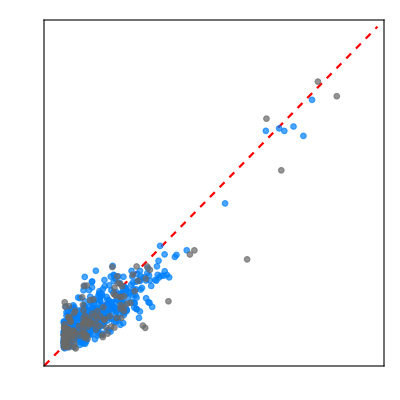

```mathematica
GPREvalPlot = Show[
(*SmoothDensityHistogram[evalRFRCorner, PlotRangePadding->None, PlotRange->All, ColorFunction->"LightTerrain"],*)
(*SmoothDensityHistogram[evalGPRTrain, PlotRangePadding->None,PlotRange->{{-0.05,0.6}, {-0.05, 0.6}}, ColorFunction->"LightTerrain"],*)
Plot[x, {x, -0.05, 0.6}, PlotStyle->{Dashed, Red}, PlotRange->All],
ListPlot[evalGPRTrain⟦;;, {1, 2}⟧, PlotMarkers->{markerDisk[rfrMCol], 0.02}, PlotRange->All],
ListPlot[evalGPRTest⟦;;, {1,2}⟧, PlotMarkers->{markerDisk[fitMCol], 0.02}, PlotRange->All],

PlotRange->{{-0.02,0.6}, {-0.02, 0.6}},
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@axTicks, None}, {{#, MaTeX[#,Magnification->1.5]}&/@axTicks, None}},
FrameLabel->{MaTeX["t_{ij}^{\\text{DFT}}, \\text{eV}", Magnification->1.5], MaTeX["t_{ij}^{\\text{prediction}}, \\text{eV}", Magnification->1.5],
None(*MaTeX["\\text{Corner-sharing}", Magnification->1.5]*)},
PlotRangePadding->None,
AspectRatio->1,
ImageSize->{Automatic,verticalSize}
]
```

```mathematica
GPREvalPlotWithLegend = Overlay[{legendEval, GPREvalPlot}, Alignment->{-0.5,0.8}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/figs/gpr_eval_test_train.svg",GPREvalPlotWithLegend]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/gpr_eval_test_train.svg

```mathematica
ResidualsGPR = Table[evalGPRTest⟦i, 1⟧ - evalGPRTest⟦i, 2⟧, {i, 1, Length@evalGPRTest}];
```

```mathematica
μ = (IntegerPart[Mean[ResidualsGPR] * 10^4]/10^4)//N;
σ = (IntegerPart[StandardDeviation[ResidualsGPR] * 10^3]/10^3)//N;
errorLabel = MaTeX["\\substack{\\sigma = "<>ToString[σ 10^3]<>"\,\\text{meV}"<> " \\\\ \\mu = " <>ToString[μ 10^3]<>"\,\\text{meV}"<>"}", Magnification->2]
```

-Graphics-

```mathematica
errorDistrib =Show[
 Histogram[ResidualsGPR,40, ChartStyle->EdgeForm[None], PlotRange->{{-0.2, 0.2}, {0,25}}],
Plot[PDF[NormalDistribution[μ,σ],x],{x, -0.2, 0.2}],

PlotRange->{{-0.2, 0.2}, {0,25}},
ImageSize->200,
Frame->True,
AspectRatio->0.8,
PlotRangePadding->None,
FrameLabel->(MaTeX[#, Magnification->1.5]&)/@{"t_{ij}^{\\text{DFT}} - t_{ij}^{\\text{prediction}}\\text{, eV}", "\\text{Count}"},
FrameTicks->{{ {# ,MaTeX[#, Magnification->1.5]}&/@{0,10, 20}, None}, 
{{# ,MaTeX[#, Magnification->1.5]}&/@{-0.2, -0.1, 0, 0.1, 0.2}, None}}
];
```

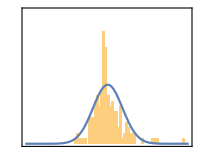
-Graphics--Graphics-

```mathematica
errorDistrbOverlay =Overlay[{
errorLabel,
errorDistrib},
Alignment->{1,1}
]
```

```mathematica
Export[NotebookDirectory[]<>"/figs/residuals.svg",errorDistrbOverlay]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/residuals.svg

```mathematica
tijsvg = MaTeX["r_{ij}, \\AA", Magnification->1.5]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/figs/auxtext.svg",tijsvg]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/auxtext.svg

### Test on HTS Cuprates

```mathematica
markerDiskWithBoundAndText[fillCol_, bondCol_, text_] := Graphics[{ fillCol,EdgeForm[{bondCol}], FaceForm[Opacity[0.3]], Disk[], Text[Style[MaTeX[text, Magnification->1], Black],{0,0}]}];
```

```mathematica
(* { Cu-Apical oxygen distance, t'_DFT / t_DFT, t'_ML / t_ML } *)
La2CuO4 = {{2.39, 112.8 / 499.9,90.185 /381.78 }};(* batch0/34332 *)
LaBa2Cu3O7 = {{2.23, 0000}};

Bi2Sr2CuO6 = {{2.59, 118.55 / 425.3,107.455 / 403.55}}; (* batch2/67426 *)

HgBa2CuO4 = {{2.79,111.3 / 431.8, 93.55 / 467.58}}; (* batch0/35943 *)
HgBa2CaCu2O6 = {{2.79, 66.33 / 417.8}};
HgBa2Ca2Cu3O8 = {{2.75, 61.18/ 440.73}};

Tl2Ba2CuO6 = {{2.699,95.5 / 319.0, 106.485 / 417.79}}; (* batch0/68582 *)
Tl2Ba2CaCu2O8 = {{2.697, 69.41 / 417.83}};
Tl2Ba2Ca2Cu3O10 = {{2.15, 85.45/ 399.86}};
```

```mathematica
HTCPlot = Show[
ListPlot[La2CuO4⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Orange, "1"], 0.05}}],
ListPlot[La2CuO4⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "1"], 0.05}}],

ListPlot[Bi2Sr2CuO6⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Orange, "2"], 0.05}}],
ListPlot[Bi2Sr2CuO6⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "2"], 0.05}}],

ListPlot[HgBa2CuO4⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Orange, "3"], 0.05}}],
ListPlot[HgBa2CuO4⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black,"3"], 0.05}}],

ListPlot[Tl2Ba2CuO6⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Orange, "4"], 0.05}}],
ListPlot[Tl2Ba2CuO6⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black,"4"], 0.05}}],


ListPlot[HgBa2CaCu2O6⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "5"], 0.05}}],
ListPlot[HgBa2Ca2Cu3O8⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "6"], 0.05}}],
ListPlot[Tl2Ba2Ca2Cu3O10⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "7"], 0.05}}],


Frame->True,
AspectRatio->1,
PlotRange->{{2.1, 2.9}, {0, 0.4}},

FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\text{Cu-Apical Oxygen Distance, \\r{A}}", "t'/t"},
FrameTicks->{
{Table[{x,MaTeX[x,Magnification->magnif]},
{x,{0, 0.1, 0.2, 0.3, 0.4, 0.5}}],
None},
{Table[{x,MaTeX[x,Magnification->magnif]},
{x, { 2.2,  2.4,  2.6, 2.8, 3}}],
None}}
];
```

```mathematica
(* make legend *)
HTClegend= PointLegend[
{Automatic,Automatic},
MaTeX[#, Magnification->magnif]&/@{
"\\text{Prediction}",
"\\text{DFT}"
},
LegendMarkers->{
markerDiskWithBound[White, Black],
markerDiskWithBound[White, Orange]
}];
```

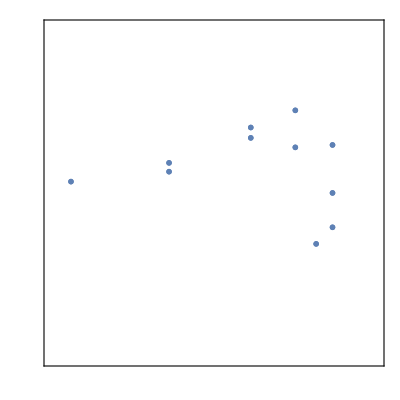

```mathematica
Overlay[{HTCPlot, HTClegend}, Alignment->{-0.3, -0.4}]
```

```mathematica
descrText = MaTeX["\\text{La}\,\\text{Bi}\,\\text{Tl}\,\\text{Hg}", Magnification->magnif]
```

-Graphics-